Deriving equation for estimating torque for an arm

```mathematica
FullSimplify[T Subscript[L, arm] Sin[ArcTan[(Subscript[L, arm] Sin[α])/(Subscript[L, arm] Cos[α] - Subscript[d, ap])] - α] + T Subscript[L, arm] Sin[ArcTan[(Subscript[L, arm] Sin[α])/(Subscript[d, ap] + Subscript[d, pdp]-Subscript[L, arm] Cos[α])] - α] + m Subscript[L, arm]/2g Cos[α]] /. {Subscript[L,arm]->Larm,Subscript[d,ap]->dap,Subscript[d,pdp]->dpdp}
```

1/2 Larm (g m Cos[α]-2 T (Sin[α+ArcTan[(Larm Sin[α])/(dap-Larm Cos[α])]]+Sin[α-ArcTan[(Larm Sin[α])/(dap+dpdp-Larm Cos[α])]]))

```mathematica
Torque[α_, Larm_, dap_, dpdp_]:=1/2 Larm (g m Cos[α]-2 T (Sin[α+ArcTan[(Larm Sin[α])/(dap-Larm Cos[α])]]+Sin[α-ArcTan[(Larm Sin[α])/(dap+dpdp-Larm Cos[α])]]))
```

If we assume around 250 N of tension at the stake rail and estimate the hytorc gearing to be about 5000 and cap the maximum motor torque at 200 mNm, we can calculate the percent power needed to move the arm at the ends. Notice that its quite small, thus ensuring that we can accurately control our arm position without having to account for the changing tension throughout the arm transition.

```mathematica
(Torque[109 * Pi / 180, 0.25, 0.2, 0.1542] /. {g -> 9.8, m -> .35, T -> 250}) / 5000 / 0.2
```

-0.0939452

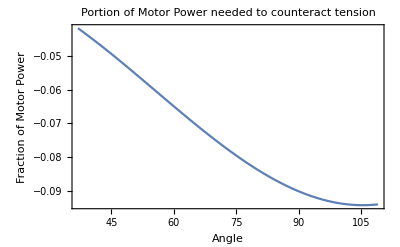

```mathematica
Plot[(Torque[α* Pi / 180, 0.25, 0.2, 0.1542] /. {g -> 9.8, m -> .35, T -> 250})/ 5000 / 0.2, {α, 37, 109}, PlotLabel-> "Portion of Motor Power needed to counteract tension",Frame-> True,  FrameLabel->{"Angle","Fraction of Motor Power"}]
```

```mathematica
Subscript[y, min] = 0.5;
Subscript[L, c0]=20.5;
g = 9.8;
Subscript[m, s]= 16;
Subscript[L, cxs]=0.24;
```

```mathematica
endtension = {(g Subscript[L, cxs] Subscript[m, s] (Subscript[L, cs]-Subscript[x, s]))/(y Subscript[L, cs])/. {Subscript[x, s] -> √(Subscript[L, cxs]^2-((-Subscript[L, c]^2+Subscript[L, cs]^2+2 Subscript[L, c] Subscript[L, cxs])^2)/(4 Subscript[L, cs]^2)), y -> (-Subscript[L, c]^2+Subscript[L, cs]^2+2 Subscript[L, c] Subscript[L, cxs])/(2 Subscript[L, cs])}}/.{Subscript[L, c]->Sqrt[Subscript[L, cs]^2 + 4 * Subscript[y, min]^2]}
```

{(75.264 (L_cs-√(0.0576-((-1.+0.48 √(1.+L_cs^2))^2)/(4 L_cs^2))))/(-1.+0.48 √(1.+L_cs^2))}

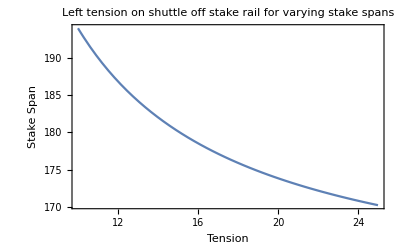

```mathematica
Plot[endtension, {Subscript[L, cs], 10, 25}, PlotLabel-> "Left tension on shuttle off stake rail for varying stake spans",Frame-> True,  FrameLabel->{"Tension","Stake Span"}]
```

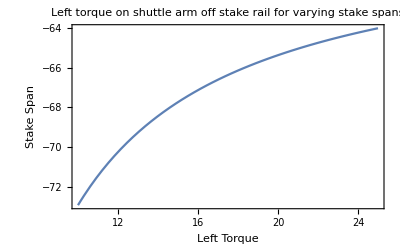

```mathematica
Plot[Torque[109 * Pi / 180, 0.25, 0.2, 0.1542] /. {g -> 9.8, m -> .35, T -> endtension}, {Subscript[L, cs], 10, 25}, PlotLabel-> "Left torque on shuttle arm off stake rail for varying stake spans",Frame-> True,  FrameLabel->{"Left Torque","Stake Span"}]
```

We can see that changing the stake spans will have negligible effect on the amount of torque needed to be exerted to control arm positions